```mathematica
Clear["Global`*"]
```

## Evolution of resistance against the least beneficial plasmid (never works)

## Dynamics

```mathematica
dSdt=b[S](1-κ 𝒩)S+γ[G1]IG1+γ[G2]IG2-(d+(1-pi[G1])ψ[G1]+(1-pi[G2])ψ[G2])S;
dG1dt=b[G1](1-κ 𝒩)IG1+(1-pi[G1])ψ[G1]S-(d[G1]+γ[G1]+σ(1-pi[G2])ψ[G2])IG1+γ[G2]IG1G2;
dG2dt=b[G2](1-κ 𝒩)IG2+(1-pi[G2])ψ[G2]S-(d[G2]+γ[G2]+σ(1-pi[G1])ψ[G1])IG2+γ[G1]IG1G2;
dG1dt=b[G1G2](1-κ 𝒩)IG1G2+σ(1-pi[G1])ψ[G1]IG2+σ(1-pi[G2])ψ[G2]IG1-(d[G1G2]+γ[G1]+γ[G2])IG1G2;
```

## Invasion analysis

Fecundity function is b:=F_i b_max Exp[-c pi[x]]

Mutant fecundity matrix Fm - all classes express the resistance π_G1^m when it comes to fecundity.

```mathematica
Fm=(1-κ 𝒩){{bm[S],0,0,0},{0,bm[G1],0,0},{0,0,bm[G2],0},{0,0,0,bm[G1G2]}}/.bm[x_]->F[x]bmax Exp[-c (pi[G1]+pi[G2])]
```

{{bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[S],0,0,0},{0,bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G1],0,0},{0,0,bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G2],0},{0,0,0,bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G1G2]}}

```mathematica
Vm=-{{-(d+(1-pi[G1])ψ[G1]+(1-pi[G2])ψ[G2]),γ[G1],γ[G2],0},
{(1-pi[G1])ψ[G1],-(d[G1]+γ[G1]+σ(1-pi[G2])ψ[G2]),0,γ[G2]},
{(1-pi[G2])ψ[G2],0,-(d[G2]+γ[G2]+σ(1-pi[G1])ψ[G1]),γ[G1]},
{0,σ(1-pi[G2])ψ[G2],σ(1-pi[G1])ψ[G1],-(d[G1G2]+γ[G1]+γ[G2])}
}
```

{{d+(1-pi[G1]) ψ[G1]+(1-pi[G2]) ψ[G2],-γ[G1],-γ[G2],0},{-((1-pi[G1]) ψ[G1]),d[G1]+γ[G1]+σ (1-pi[G2]) ψ[G2],0,-γ[G2]},{-((1-pi[G2]) ψ[G2]),0,d[G2]+γ[G2]+σ (1-pi[G1]) ψ[G1],-γ[G1]},{0,-σ (1-pi[G2]) ψ[G2],-σ (1-pi[G1]) ψ[G1],d[G1G2]+γ[G1]+γ[G2]}}

```mathematica
Vm//MatrixForm
```

(d+(1-pi[G1]) ψ[G1]+(1-pi[G2]) ψ[G2] | -γ[G1] | -γ[G2] | 0
-((1-pi[G1]) ψ[G1]) | d[G1]+γ[G1]+σ (1-pi[G2]) ψ[G2] | 0 | -γ[G2]
-((1-pi[G2]) ψ[G2]) | 0 | d[G2]+γ[G2]+σ (1-pi[G1]) ψ[G1] | -γ[G1]
0 | -σ (1-pi[G2]) ψ[G2] | -σ (1-pi[G1]) ψ[G1] | d[G1G2]+γ[G1]+γ[G2])

```mathematica
Bm=Fm -Vm//Simplify;
```

```mathematica
Bm//Simplify//MatrixForm
```

(-d+bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[S]+(-1+pi[G1]) ψ[G1]+(-1+pi[G2]) ψ[G2] | γ[G1] | γ[G2] | 0
-((-1+pi[G1]) ψ[G1]) | -d[G1]+ⅇ^(-c (pi[G1]+pi[G2])) (bmax-bmax 𝒩 κ) F[G1]-γ[G1]+σ (-1+pi[G2]) ψ[G2] | 0 | γ[G2]
-((-1+pi[G2]) ψ[G2]) | 0 | -d[G2]+ⅇ^(-c (pi[G1]+pi[G2])) (bmax-bmax 𝒩 κ) F[G2]-γ[G2]+σ (-1+pi[G1]) ψ[G1] | γ[G1]
0 | -σ (-1+pi[G2]) ψ[G2] | -σ (-1+pi[G1]) ψ[G1] | -d[G1G2]+ⅇ^(-c (pi[G1]+pi[G2])) (bmax-bmax 𝒩 κ) F[G1G2]-γ[G1]-γ[G2])

```mathematica
D[Bm,pi[G1]]/.pi[G2]->0//MatrixForm
```

(-bmax c ⅇ^(-c pi[G1]) (1-𝒩 κ) F[S]+ψ[G1] | 0 | 0 | 0
-ψ[G1] | -c ⅇ^(-c pi[G1]) (bmax-bmax 𝒩 κ) F[G1] | 0 | 0
0 | 0 | -c ⅇ^(-c pi[G1]) (bmax-bmax 𝒩 κ) F[G2]+σ ψ[G1] | 0
0 | 0 | -σ ψ[G1] | -c ⅇ^(-c pi[G1]) (bmax-bmax 𝒩 κ) F[G1G2])

```mathematica
BmNG=Fm.Inverse[Vm];
```

```mathematica
BmNGCase1=BmNG[[1;;3,1;;3]]/.σ->0;
```

```mathematica
Eigenvalues[BmNGCase1]/.{bmax->50,d->1,d[G1]->50,d[G2]->1,κ->0.0001,pi[G1]->0.5,pi[G2]->0,γ[G1]->0.01,γ[G2]->0.01,F[S]->1.0,F[G1]->0.3,F[G2]->0.5,ψ[G1]->10,ψ[G2]->1,𝒩->9595,c->0.01}
```

{0.0120869,0.287721,0.999461}

```mathematica
{Eigenvalues[BmNGCase1],D[Eigenvalues[BmNGCase1],pi[G1]]}/.{bmax->50,d->0.1,d[G1]->50,d[G2]->1,κ->0.0001,pi[G1]->0.5,pi[G2]->0,γ[G1]->0.01,γ[G2]->0.01,F[S]->1.0,F[G1]->0.3,F[G2]->0.5,ψ[G1]->10,ψ[G2]->0.01,𝒩->9596,c->0.01}
```

{{0.0120571,0.393406,0.995044},{-0.000120417,0.765907,-0.00984722}}

```mathematica
Inverse[Vm]/.{γ[G1]->0,γ[G2]->0,σ->0,κ->0}//MatrixForm//Simplify
```

(1/(d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2]-pi[G2] ψ[G2]) | 0 | 0 | 0
-((-1+pi[G1]) ψ[G1])/(d[G1] (d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2]-pi[G2] ψ[G2])) | 1/d[G1] | 0 | 0
-((-1+pi[G2]) ψ[G2])/(d[G2] (d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2]-pi[G2] ψ[G2])) | 0 | 1/d[G2] | 0
0 | 0 | 0 | 1/d[G1G2])

```mathematica
BmNGCase1/.{γ[G1]->0,γ[G2]->0,pi[G2]->0}//Simplify//MatrixForm
```

(-(bmax ⅇ^(-c pi[G1]) (-1+𝒩 κ) F[S])/(d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2]) | 0 | 0
(bmax ⅇ^(-c pi[G1]) (-1+𝒩 κ) F[G1] (-1+pi[G1]) ψ[G1])/(d[G1] (d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2])) | (bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G1])/d[G1] | 0
-(bmax ⅇ^(-c pi[G1]) (-1+𝒩 κ) F[G2] ψ[G2])/(d[G2] (d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2])) | 0 | (bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G2])/d[G2])

```mathematica
evalsBmNGCase1=BmNGCase1/.{γ[G1]->0,γ[G2]->0}//Eigenvalues;
```

```mathematica
evalsBmNGCase1//FullSimplify
```

{(bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[S])/(d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2]-pi[G2] ψ[G2]),(bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G1])/d[G1],(bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G2])/d[G2]}

```mathematica
D[evalsBmNGCase1,pi[G1]]/.{pi[G2]->0,κ->0}//Simplify
```

{-(bmax ⅇ^(-c pi[G1]) F[S] ((-1+c-c pi[G1]) ψ[G1]+c (d+ψ[G2])))/(d+ψ[G1]-pi[G1] ψ[G1]+ψ[G2])^2,-(bmax c ⅇ^(-c pi[G1]) F[G1])/d[G1],-(bmax c ⅇ^(-c pi[G1]) F[G2])/d[G2]}

Threshold to attractor very similar to Gandon & Vale obvz, but important difference, 1st eigenvalue unlikely to be dominant, hence selection against resistance of any of the types...

```mathematica
ansπG1=Solve[(-1+c-c pi[G1]) ψ[G1]+c (d+ψ[G2])==0,pi[G1]][[1]][[1]]//Simplify
```

pi[G1]→(-1+c)/c+(d+ψ[G2])/ψ[G1]

```mathematica
Solve[(-1+c)/c+(d+ψ[G2])/ψ[G1]==1,c]//Simplify
```

{{c→ψ[G1]/(d+ψ[G2])}}

```mathematica
piold=1-1/c+d/ψ[G1]
```

1-1/c+d/ψ[G1]

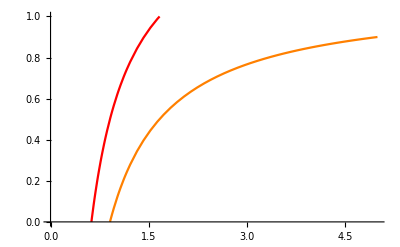

```mathematica
Plot[Evaluate[{piold,pi[G1]}/.ansπG1/.{d->1,ψ[G1]->10,ψ[G2]->5}],{c,0,5},PlotRange->{0,1},PlotStyle->{Orange,Red}]
```

```mathematica
D[evalsBmNGCase1,pi[G1],pi[G1]]/.{pi[G1]->0,pi[G2]->0}//Simplify
```

{(bmax F[S] ((2-2 c+c^2) ψ[G1]^2+2 (-1+c) c ψ[G1] (d+ψ[G2])+c^2 (d+ψ[G2])^2))/(d+ψ[G1]+ψ[G2])^3,(bmax c^2 F[G1])/d[G1],(bmax c^2 F[G2])/d[G2]}

```mathematica
BmCase1=Bm[[1;;3,1;;3]]/.{σ->0,pi[G2]->0,κ->0}//Simplify
```

{{-d+bmax ⅇ^(-c pi[G1]) F[S]+(-1+pi[G1]) ψ[G1]-ψ[G2],γ[G1],γ[G2]},{-(-1+pi[G1]) ψ[G1],-d[G1]+bmax ⅇ^(-c pi[G1]) F[G1]-γ[G1],0},{ψ[G2],0,-d[G2]+bmax ⅇ^(-c pi[G1]) F[G2]-γ[G2]}}

```mathematica
BmCase1//MatrixForm
```

(-d+bmax ⅇ^(-c pi[G1]) F[S]+(-1+pi[G1]) ψ[G1]-ψ[G2] | γ[G1] | γ[G2]
-(-1+pi[G1]) ψ[G1] | -d[G1]+bmax ⅇ^(-c pi[G1]) F[G1]-γ[G1] | 0
ψ[G2] | 0 | -d[G2]+bmax ⅇ^(-c pi[G1]) F[G2]-γ[G2])

```mathematica
BmCase1MainResult=BmCase1/.{γ[G1]->0,γ[G2]->0}//Eigenvalues//Simplify
```

{-d[G1]+bmax ⅇ^(-c pi[G1]) F[G1],-d[G2]+bmax ⅇ^(-c pi[G1]) F[G2],-d+bmax ⅇ^(-c pi[G1]) F[S]+(-1+pi[G1]) ψ[G1]-ψ[G2]}

```mathematica
BmCase1MainResult/.{F[S]->0,pi[G1]->0}//Simplify
```

{-d[G1]+bmax F[G1],-d[G2]+bmax F[G2],-d-ψ[G1]-ψ[G2]}

```mathematica
D[BmCase1MainResult,pi[G1]]/.{pi[G1]->0,F[S]->0}//Simplify
```

{-bmax c F[G1],-bmax c F[G2],ψ[G1]}

```mathematica
evalx=BmCase1//Eigenvalues;
```

```mathematica
selgrad=D[evalx,pi[G1]]/.{pi[G1]->0,F[G2]->F[G1]+δ,γ[G1]->0,γ[G2]->0,ψ[G1]->ψ,ψ[G2]->ψ,d[G1]->d,d[G2]->d,F[S]->0}//Simplify;
```

```mathematica
selgrad[[1]]//Variables
```

{bmax,c,d,δ,ψ,F[G1]}

```mathematica
selgrad[[1]]
```

-c Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]-(3 c d^3-d^2 ψ+6 c d^2 ψ-2 bmax c d^2 F[G1]+bmax d ψ F[G1]-4 bmax c d ψ F[G1]-2 bmax c d^2 (δ+F[G1])+bmax d ψ (δ+F[G1])-4 bmax c d ψ (δ+F[G1])+bmax^2 c d F[G1] (δ+F[G1])-bmax^2 ψ F[G1] (δ+F[G1])+2 bmax^2 c ψ F[G1] (δ+F[G1])+(-2 d ψ+bmax δ ψ+c (6 d^2-2 bmax d δ+8 d ψ-2 bmax δ ψ)+2 bmax (ψ-2 c (d+ψ)) F[G1]) Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]+(3 c d-ψ+2 c ψ) Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]^2)/(3 d^2+4 d ψ-2 bmax d F[G1]-2 bmax ψ F[G1]-2 bmax d (δ+F[G1])-2 bmax ψ (δ+F[G1])+bmax^2 F[G1] (δ+F[G1])+2 (3 d-bmax δ+2 ψ-2 bmax F[G1]) Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]+3 Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]^2)

```mathematica
domeval=evalx/.{pi[G1]->0,F[G2]->F[G1]+δ,γ[G1]->0,γ[G2]->0,ψ[G1]->ψ,ψ[G2]->ψ,d[G1]->d,d[G2]->d,F[S]->0,bmax->50,c->1}/.{F[G1]->1,d->50}//Simplify
```

{Root[(-2500 δ-100 δ ψ) #1+(50-50 δ+2 ψ) #1^2+#1^3&,1],Root[(-2500 δ-100 δ ψ) #1+(50-50 δ+2 ψ) #1^2+#1^3&,2],Root[(-2500 δ-100 δ ψ) #1+(50-50 δ+2 ψ) #1^2+#1^3&,3]}

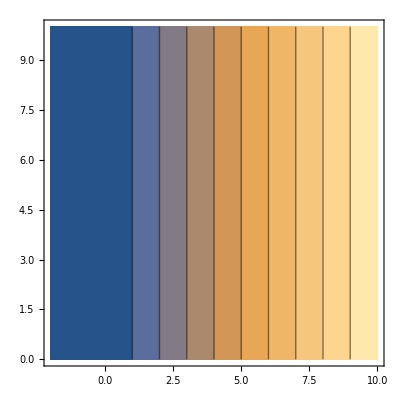

```mathematica
ContourPlot[domeval[[3]],{δ,-2,10},{ψ,0,10}]
```

```mathematica
ContourPlot[selgrad[[3]]/.{bmax->50,c->1,d->50,F[G1]->1},{δ,-2,10},{ψ,0,10}]
```

-Graphics-

```mathematica
ContourPlot[selgrad[[2]]/.{bmax->50,c->1,d->50,F[G1]->1},{δ,-2,10},{ψ,0,10}]
```

-Graphics-